```mathematica
required: system of 2 quads and 1 payload
```

system elements :
quad 1 - given as system input. x,y coor. θ is not influential
quad 2  - given as system input. x,y coor. θ is not influential
payload (contrained to quads locations)

```mathematica
Quit[]
```

```mathematica
Needs["VariationalMethods`"]
```

kinematics :

```mathematica
prop2D={(Subscript[X, i]=({{Subscript[x, i][t]}, {Subscript[y, i][t]}, {0}}))//MatrixForm//TraditionalForm,
(Subscript[Imat, i]=({{Subscript[I, i,xx], 0, 0}, {0, Subscript[I, i,yy], 0}, {0, 0, Subscript[I, i,zz]}}))//MatrixForm//TraditionalForm,
Subscript[ω, i]=D[{0,0,Subscript[θ, i][t]},t]}
prop2D/.i->1
prop2D/.i->2
prop2D/.i->p
```

{(x_i(t)
y_i(t)
0),(ⅈ_(i,xx) | 0 | 0
0 | ⅈ_(i,yy) | 0
0 | 0 | ⅈ_(i,zz)),{0,0,θ_i'[t]}}

{(x_1(t)
y_1(t)
0),(ⅈ_(1,xx) | 0 | 0
0 | ⅈ_(1,yy) | 0
0 | 0 | ⅈ_(1,zz)),{0,0,θ_1'[t]}}

{(x_2(t)
y_2(t)
0),(ⅈ_(2,xx) | 0 | 0
0 | ⅈ_(2,yy) | 0
0 | 0 | ⅈ_(2,zz)),{0,0,θ_2'[t]}}

{(x_p(t)
y_p(t)
0),(ⅈ_(p,xx) | 0 | 0
0 | ⅈ_(p,yy) | 0
0 | 0 | ⅈ_(p,zz)),{0,0,θ_p'[t]}}

```mathematica
(Subscript[v, i]=D[Subscript[X, i],t])//MatrixForm//TraditionalForm
Subscript[v, i]/.i->1
Subscript[v, i]/.i->2
Subscript[v, i]/.i->p
```

(x_i'(t)
y_i'(t)
0)

{{x_1'[t]},{y_1'[t]},{0}}

{{x_2'[t]},{y_2'[t]},{0}}

{{x_p'[t]},{y_p'[t]},{0}}

rotations :

```mathematica
(*(Rp2I=(RotationMatrix[Subscript[θ, p]]))//MatrixForm;
HangPoint1=PayloadCenterPos-Rp2I.{Subscript[l, p]/2,-Subscript[h, p]/2}
HangPoint2=PayloadCenterPos+Rp2I.{Subscript[l, p]/2,Subscript[h, p]/2}

Quad1CenterPos = {Subscript[x, i],Subscript[z, i]} /. i->1
Quad2CenterPos = {Subscript[x, i],Subscript[z, i]} /. i->2
PayloadCenterPos = {Subscript[x, i],Subscript[z, i]} /. i->p
Subscript[Δ, 1]=({{Subscript[x, 1]}, {Subscript[y, 1]}})-({{Subscript[x, p]}, {Subscript[y, p]}})-Rp2I.{Subscript[l, p]/2,-Subscript[h, p]/2}*)
```

{3.98866,4.52335}

{5.22548,6.09506}

{0,10}

{10,10}

{5,5}

{{-6.01134},{-0.476653+y_1-y_p}}

enrgies :

```mathematica
Imat
Subscript[Imat, i]
Subscript[Imat, i]/.i->1
```

Imat

{{ⅈ_(i,xx),0,0},{0,ⅈ_(i,yy),0},{0,0,ⅈ_(i,zz)}}

{{ⅈ_(1,xx),0,0},{0,ⅈ_(1,yy),0},{0,0,ⅈ_(1,zz)}}

```mathematica
a[e]
a[e]/.a[a_]->Cos[a]
a[e]/.a->Cos
```

a[e]

Cos[e]

Cos[e]

```mathematica
dispSimp = {a_[t]->a,Cos[a_]->c[a],Sin[a_]->s[a],Subscript[ⅈ, i_,zz]->Subscript[I, i]};
```

```mathematica
{(Rp2I=RotationMatrix[Subscript[θ, p][t]])//MatrixForm,
x1dotSqr=(Transpose[Subscript[v, i]].Subscript[v, i])[[1,1]]/.i->1,
x2dotSqr=(Transpose[Subscript[v, i]].Subscript[v, i])[[1,1]]/.i->2,
IωSqr1=Subscript[ω, i].Subscript[Imat, i] .Subscript[ω, i]/.i->1,
IωSqr2=Subscript[ω, i].Subscript[Imat, i] .Subscript[ω, i]/.i->2,
xpdotSqr=(Transpose[Subscript[v, i]].Subscript[v, i])[[1,1]]/.i->p,
IωSqrp=Subscript[ω, i].Subscript[Imat, i] .Subscript[ω, i]/.i->p,
Subscript[r, 1][t]=({{Subscript[x, 1][t]}, {Subscript[y, 1][t]}})-(({{Subscript[x, p][t]}, {Subscript[y, p][t]}})-Rp2I.{Subscript[l, p]/2,-Subscript[h, p]/2}),
Subscript[r, 2][t]=({{Subscript[x, 2][t]}, {Subscript[y, 2][t]}})-(({{Subscript[x, p][t]}, {Subscript[y, p][t]}})+Rp2I.{Subscript[l, p]/2,Subscript[h, p]/2}),
Subscript[Δ, 1]=√((Subscript[r, 1][t][[1]])^2+(Subscript[r, 1][t][[2]])^2)-Subscript[L0, 1],

Subscript[Δ, 2]=√((Subscript[r, 2][t][[1]])^2+(Subscript[r, 2][t][[2]])^2)-Subscript[L0, 2]};
(T=1/2 Subscript[m, 1] x1dotSqr+1/2 IωSqr1+1/2 Subscript[m, 2] x2dotSqr+1/2 IωSqr2+1/2 Subscript[m, p] xpdotSqr+1/2 IωSqrp);
(*Subscript[r, i]=Subscript[l, i]+Δl*)
V=Subscript[m, 1] g(Subscript[X, i][[2]]/.i->1)+Subscript[m, 2] g(Subscript[X, i][[2]]/.i->2)+Subscript[m, p] g(Subscript[X, i][[2]]/.i->p)+1/2 Subscript[k, 1] Subscript[Δ, 1]^2+1/2 Subscript[k, 2] Subscript[Δ, 2]^2;
L=(T-V); (*Subscript[T, quad#1]+Subscript[T, quad#2]+Subscript[T, payload] - (Subscript[V, quad#1]+Subscript[V, quad#2]+Subscript[V, payload]+Subscript[V, spring#1]+Subscript[V, spring#2])*)
L=(T-V)[[1]]
```

-g m_1 y_1[t]-g m_2 y_2[t]-1/2 k_1 (-L0_1+√((1/2 Sin[θ_p[t]] h_p+1/2 Cos[θ_p[t]] l_p+x_1[t]-x_p[t])^2+(-1/2 Cos[θ_p[t]] h_p+1/2 Sin[θ_p[t]] l_p+y_1[t]-y_p[t])^2))^2-1/2 k_2 (-L0_2+√((1/2 Sin[θ_p[t]] h_p-1/2 Cos[θ_p[t]] l_p+x_2[t]-x_p[t])^2+(-1/2 Cos[θ_p[t]] h_p-1/2 Sin[θ_p[t]] l_p+y_2[t]-y_p[t])^2))^2-g m_p y_p[t]+1/2 m_1 (x_1'[t]^2+y_1'[t]^2)+1/2 m_2 (x_2'[t]^2+y_2'[t]^2)+1/2 m_p (x_p'[t]^2+y_p'[t]^2)+1/2 ⅈ_(1,zz) θ_1'[t]^2+1/2 ⅈ_(2,zz) θ_2'[t]^2+1/2 ⅈ_(p,zz) θ_p'[t]^2

```mathematica
L//.dispSimp//TraditionalForm
```

-1/2 k_1 (√((1/2 l_p c(θ_p)+1/2 h_p s(θ_p)-x_p+x_1)^2+(-1/2 h_p c(θ_p)+1/2 l_p s(θ_p)-y_p+y_1)^2)-L0_1)^2-1/2 k_2 (√((-1/2 l_p c(θ_p)+1/2 h_p s(θ_p)-x_p+x_2)^2+(-1/2 h_p c(θ_p)-1/2 l_p s(θ_p)-y_p+y_2)^2)-L0_2)^2-g m_p y_p-g m_1 y_1-g m_2 y_2+1/2 ⅈ_1 (θ_1')^2+1/2 ⅈ_2 (θ_2')^2+1/2 m_p ((x_p')^2+(y_p')^2)+1/2 m_1 ((x_1')^2+(y_1')^2)+1/2 m_2 ((x_2')^2+(y_2')^2)+1/2 ⅈ_p (θ_p')^2

```mathematica
(*q=({{Subscript[x, 1]}, {Subscript[y, 1]}, {Subscript[θ, 1]}, {Subscript[x, 2]}, {Subscript[y, 2]}, {Subscript[θ, 2]}, {Subscript[x, p]}, {Subscript[y, p]}, {Subscript[θ, p]}})[t]
({{Subscript[x, p]}, {Subscript[y, p]}, {Subscript[θ, p]}})*)
```

{{x_1},{y_1},{θ_1},{x_2},{y_2},{θ_2},{x_p},{y_p},{θ_p}}[t]

after setting L calculate the lagrangian derivatives and equations:

```mathematica
(quadEqNominal=EulerEquations[L,{Subscript[x, 1][t],Subscript[y, 1][t],Subscript[θ, 1][t],Subscript[x, 2][t],Subscript[y, 2][t],Subscript[θ, 2][t],Subscript[x, p][t],Subscript[y, p][t],Subscript[θ, p][t]},t](*[[All,1]]*)(*==Q*)//Simplify)//MatrixForm//TraditionalForm
```

((k_1 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t)) (√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2)-L0_1))/(2 √(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2))+m_1 x_1''(t)==0
g m_1+(k_1 (-1/2 h_p cos(θ_p(t))+1/2 l_p sin(θ_p(t))-y_p(t)+y_1(t)) (√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2)-L0_1))/(√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2))+m_1 y_1''(t)==0
ⅈ_(1,zz) θ_1''(t)==0
(k_2 (1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t)) (√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2)-L0_2))/(√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2))+m_2 x_2''(t)==0
g m_2+(k_2 (-1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))-y_p(t)+y_2(t)) (√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2)-L0_2))/(√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2))+m_2 y_2''(t)==0
ⅈ_(2,zz) θ_2''(t)==0
(k_1 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t)) (√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2)-L0_1))/(2 √(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2))+(k_2 (1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t)) (√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2)-L0_2))/(√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2))==m_p x_p''(t)
(k_1 (-1/2 h_p cos(θ_p(t))+1/2 l_p sin(θ_p(t))-y_p(t)+y_1(t)) (√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2)-L0_1))/(√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2))+(k_2 (-1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))-y_p(t)+y_2(t)) (√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2)-L0_2))/(√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2))==m_p (g+y_p''(t))
ⅈ_(p,zz) θ_p''(t)+(k_1 (h_p (x_1(t) cos(θ_p(t))-x_p(t) cos(θ_p(t))+(y_1(t)-y_p(t)) sin(θ_p(t)))+l_p (x_1(t) (-sin(θ_p(t)))+x_p(t) sin(θ_p(t))+(y_1(t)-y_p(t)) cos(θ_p(t)))) (√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2)-L0_1))/(2 √(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2))+(k_2 (h_p (x_2(t) cos(θ_p(t))-x_p(t) cos(θ_p(t))+(y_2(t)-y_p(t)) sin(θ_p(t)))+l_p (x_2(t) sin(θ_p(t))-x_p(t) sin(θ_p(t))+(y_p(t)-y_2(t)) cos(θ_p(t)))) (√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2)-L0_2))/(2 √((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2))==0)

```mathematica
(quadEqNominal=EulerEquations[L,{(*Subscript[x, 1][t],Subscript[y, 1][t],Subscript[θ, 1][t],Subscript[x, 2][t],Subscript[y, 2][t],Subscript[θ, 2][t],*)Subscript[x, p][t],Subscript[y, p][t],Subscript[θ, p][t]},t](*[[All,1]]*)(*==Q*)//Simplify)//MatrixForm//TraditionalForm
```

((k_1 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t)) (√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2)-L0_1))/(2 √(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2))+(k_2 (1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t)) (√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2)-L0_2))/(√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2))==m_p x_p''(t)
(k_1 (-1/2 h_p cos(θ_p(t))+1/2 l_p sin(θ_p(t))-y_p(t)+y_1(t)) (√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2)-L0_1))/(√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2))+(k_2 (-1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))-y_p(t)+y_2(t)) (√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2)-L0_2))/(√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2))==m_p (g+y_p''(t))
ⅈ_(p,zz) θ_p''(t)+(k_1 (h_p (x_1(t) cos(θ_p(t))-x_p(t) cos(θ_p(t))+(y_1(t)-y_p(t)) sin(θ_p(t)))+l_p (x_1(t) (-sin(θ_p(t)))+x_p(t) sin(θ_p(t))+(y_1(t)-y_p(t)) cos(θ_p(t)))) (√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2)-L0_1))/(2 √(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2))+(k_2 (h_p (x_2(t) cos(θ_p(t))-x_p(t) cos(θ_p(t))+(y_2(t)-y_p(t)) sin(θ_p(t)))+l_p (x_2(t) sin(θ_p(t))-x_p(t) sin(θ_p(t))+(y_p(t)-y_2(t)) cos(θ_p(t)))) (√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2)-L0_2))/(2 √((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2))==0)

```mathematica
quadEqNominal //MatrixForm
```

((k_1 (Sin[θ_p[t]] h_p+Cos[θ_p[t]] l_p+2 x_1[t]-2 x_p[t]) (-L0_1+√(1/4 (Sin[θ_p[t]] h_p+Cos[θ_p[t]] l_p+2 x_1[t]-2 x_p[t])^2+(1/2 Cos[θ_p[t]] h_p-1/2 Sin[θ_p[t]] l_p-y_1[t]+y_p[t])^2)))/(2 √(1/4 (Sin[θ_p[t]] h_p+Cos[θ_p[t]] l_p+2 x_1[t]-2 x_p[t])^2+(1/2 Cos[θ_p[t]] h_p-1/2 Sin[θ_p[t]] l_p-y_1[t]+y_p[t])^2))+(k_2 (1/2 Sin[θ_p[t]] h_p-1/2 Cos[θ_p[t]] l_p+x_2[t]-x_p[t]) (-L0_2+√((1/2 Sin[θ_p[t]] h_p-1/2 Cos[θ_p[t]] l_p+x_2[t]-x_p[t])^2+1/4 (Cos[θ_p[t]] h_p+Sin[θ_p[t]] l_p-2 y_2[t]+2 y_p[t])^2)))/(√((1/2 Sin[θ_p[t]] h_p-1/2 Cos[θ_p[t]] l_p+x_2[t]-x_p[t])^2+1/4 (Cos[θ_p[t]] h_p+Sin[θ_p[t]] l_p-2 y_2[t]+2 y_p[t])^2))==m_p x_p''[t]
(k_1 (-1/2 Cos[θ_p[t]] h_p+1/2 Sin[θ_p[t]] l_p+y_1[t]-y_p[t]) (-L0_1+√(1/4 (Sin[θ_p[t]] h_p+Cos[θ_p[t]] l_p+2 x_1[t]-2 x_p[t])^2+(1/2 Cos[θ_p[t]] h_p-1/2 Sin[θ_p[t]] l_p-y_1[t]+y_p[t])^2)))/(√(1/4 (Sin[θ_p[t]] h_p+Cos[θ_p[t]] l_p+2 x_1[t]-2 x_p[t])^2+(1/2 Cos[θ_p[t]] h_p-1/2 Sin[θ_p[t]] l_p-y_1[t]+y_p[t])^2))+(k_2 (-1/2 Cos[θ_p[t]] h_p-1/2 Sin[θ_p[t]] l_p+y_2[t]-y_p[t]) (-L0_2+√((1/2 Sin[θ_p[t]] h_p-1/2 Cos[θ_p[t]] l_p+x_2[t]-x_p[t])^2+1/4 (Cos[θ_p[t]] h_p+Sin[θ_p[t]] l_p-2 y_2[t]+2 y_p[t])^2)))/(√((1/2 Sin[θ_p[t]] h_p-1/2 Cos[θ_p[t]] l_p+x_2[t]-x_p[t])^2+1/4 (Cos[θ_p[t]] h_p+Sin[θ_p[t]] l_p-2 y_2[t]+2 y_p[t])^2))==m_p (g+y_p''[t])
(k_1 (l_p (-Sin[θ_p[t]] x_1[t]+Sin[θ_p[t]] x_p[t]+Cos[θ_p[t]] (y_1[t]-y_p[t]))+h_p (Cos[θ_p[t]] x_1[t]-Cos[θ_p[t]] x_p[t]+Sin[θ_p[t]] (y_1[t]-y_p[t]))) (-L0_1+√(1/4 (Sin[θ_p[t]] h_p+Cos[θ_p[t]] l_p+2 x_1[t]-2 x_p[t])^2+(1/2 Cos[θ_p[t]] h_p-1/2 Sin[θ_p[t]] l_p-y_1[t]+y_p[t])^2)))/(2 √(1/4 (Sin[θ_p[t]] h_p+Cos[θ_p[t]] l_p+2 x_1[t]-2 x_p[t])^2+(1/2 Cos[θ_p[t]] h_p-1/2 Sin[θ_p[t]] l_p-y_1[t]+y_p[t])^2))+(k_2 (h_p (Cos[θ_p[t]] x_2[t]-Cos[θ_p[t]] x_p[t]+Sin[θ_p[t]] (y_2[t]-y_p[t]))+l_p (Sin[θ_p[t]] x_2[t]-Sin[θ_p[t]] x_p[t]+Cos[θ_p[t]] (-y_2[t]+y_p[t]))) (-L0_2+√((1/2 Sin[θ_p[t]] h_p-1/2 Cos[θ_p[t]] l_p+x_2[t]-x_p[t])^2+1/4 (Cos[θ_p[t]] h_p+Sin[θ_p[t]] l_p-2 y_2[t]+2 y_p[t])^2)))/(2 √((1/2 Sin[θ_p[t]] h_p-1/2 Cos[θ_p[t]] l_p+x_2[t]-x_p[t])^2+1/4 (Cos[θ_p[t]] h_p+Sin[θ_p[t]] l_p-2 y_2[t]+2 y_p[t])^2))+ⅈ_(p,zz) θ_p''[t]==0)

```mathematica
terms={
(*√(1/4 (Sin[Subscript[θ, p][t]] Subscript[h, p]+Cos[Subscript[θ, p][t]] Subscript[l, p]+2 Subscript[x, 1][t]-2 Subscript[x, p][t])^2+(1/2 Cos[Subscript[θ, p][t]] Subscript[h, p]-1/2 Sin[Subscript[θ, p][t]] Subscript[l, p]-Subscript[y, 1][t]+Subscript[y, p][t])^2)->dom1,*)
1/4 (Sin[Subscript[θ, p][t]] Subscript[h, p]+Cos[Subscript[θ, p][t]] Subscript[l, p]+2 Subscript[x, 1][t]-2 Subscript[x, p][t])^2+(1/2 Cos[Subscript[θ, p][t]] Subscript[h, p]-1/2 Sin[Subscript[θ, p][t]] Subscript[l, p]-Subscript[y, 1][t]+Subscript[y, p][t])^2->dom11,
(*√((1/2 Sin[Subscript[θ, p][t]] Subscript[h, p]-1/2 Cos[Subscript[θ, p][t]] Subscript[l, p]+Subscript[x, 2][t]-Subscript[x, p][t])^2+1/4 (Cos[Subscript[θ, p][t]] Subscript[h, p]+Sin[Subscript[θ, p][t]] Subscript[l, p]-2 Subscript[y, 2][t]+2 Subscript[y, p][t])^2)->dom2,*)
(1/2 Sin[Subscript[θ, p][t]] Subscript[h, p]-1/2 Cos[Subscript[θ, p][t]] Subscript[l, p]+Subscript[x, 2][t]-Subscript[x, p][t])^2+1/4 (Cos[Subscript[θ, p][t]] Subscript[h, p]+Sin[Subscript[θ, p][t]] Subscript[l, p]-2 Subscript[y, 2][t]+2 Subscript[y, p][t])^2->dom22
};
```

```mathematica
terms2={
 (Sin[Subscript[θ, p][t]] Subscript[h, p]+Cos[Subscript[θ, p][t]] Subscript[l, p]+2 Subscript[x, 1][t]-2 Subscript[x, p][t])^1->(2 r1x),(-1/2 Cos[Subscript[θ, p][t]] Subscript[h, p]+1/2 Sin[Subscript[θ, p][t]] Subscript[l, p]+Subscript[y, 1][t]-Subscript[y, p][t])^1->r1y,
1/2 Cos[Subscript[θ, p][t]] Subscript[h, p]-1/2 Sin[Subscript[θ, p][t]] Subscript[l, p]-Subscript[y, 1][t]+Subscript[y, p][t]->-r1y,
(1/2 Sin[Subscript[θ, p][t]] Subscript[h, p]-1/2 Cos[Subscript[θ, p][t]] Subscript[l, p]+Subscript[x, 2][t]-Subscript[x, p][t])^1->r2x, (-1/2 Cos[Subscript[θ, p][t]] Subscript[h, p]-1/2 Sin[Subscript[θ, p][t]] Subscript[l, p]+Subscript[y, 2][t]-Subscript[y, p][t])^1->r2y,
Cos[Subscript[θ, p][t]] Subscript[h, p]+Sin[Subscript[θ, p][t]] Subscript[l, p]-2 Subscript[y, 2][t]+2 Subscript[y, p][t]->(-2 r2y),
Subscript[l, p] (-Sin[Subscript[θ, p][t]] Subscript[x, 1][t]+Sin[Subscript[θ, p][t]] Subscript[x, p][t]+Cos[Subscript[θ, p][t]] (Subscript[y, 1][t]-Subscript[y, p][t]))->dr1,
Subscript[h, p] (Cos[Subscript[θ, p][t]] Subscript[x, 1][t]-Cos[Subscript[θ, p][t]] Subscript[x, p][t]+Sin[Subscript[θ, p][t]] (Subscript[y, 1][t]-Subscript[y, p][t]))->dr2,
Subscript[h, p] (Cos[Subscript[θ, p][t]] Subscript[x, 2][t]-Cos[Subscript[θ, p][t]] Subscript[x, p][t]+Sin[Subscript[θ, p][t]] (Subscript[y, 2][t]-Subscript[y, p][t]))->dr4,
Subscript[l, p] (Sin[Subscript[θ, p][t]] Subscript[x, 2][t]-Sin[Subscript[θ, p][t]] Subscript[x, p][t]+Cos[Subscript[θ, p][t]] (-Subscript[y, 2][t]+Subscript[y, p][t]))->dr3
};
```

```mathematica
(simpStep1=(quadEqNominal//Simplify)/.terms2)(*//.dispSimp*)(*//Simplify*)//MatrixForm(*//TraditionalForm*)
```

((r1x k_1 (√(r1x^2+r1y^2)-L0_1))/(√(r1x^2+r1y^2))+(r2x k_2 (√(r2x^2+r2y^2)-L0_2))/(√(r2x^2+r2y^2))==m_p x_p''[t]
(r1y k_1 (√(r1x^2+r1y^2)-L0_1))/(√(r1x^2+r1y^2))+(r2y k_2 (√(r2x^2+r2y^2)-L0_2))/(√(r2x^2+r2y^2))==m_p (g+y_p''[t])
((dr1+dr2) k_1 (√(r1x^2+r1y^2)-L0_1))/(2 √(r1x^2+r1y^2))+((dr3+dr4) k_2 (√(r2x^2+r2y^2)-L0_2))/(2 √(r2x^2+r2y^2))+ⅈ_(p,zz) θ_p''[t]==0)

```mathematica
terms3={
√(r1x^2+r1y^2)->a,
√(r2x^2+r2y^2)->b,
(dr1+dr2)->(2c1),
(dr3+dr4)->(2 c2),
r1x^2+r1y^2->a^2,r2x^2+r2y^2->b^2,
√(a^2)->a,√(b^2)->b}
```

{√(r1x^2+r1y^2)→a,√(r2x^2+r2y^2)→b,dr1+dr2→2 c1,dr3+dr4→2 c2,r1x^2+r1y^2→a^2,r2x^2+r2y^2→b^2,√(a^2)→a,√(b^2)→b}

```mathematica
(*simpStep1//InputForm*)
```

{(r1x*Subscript[k, 1]*(Sqrt[r1x^2 + r1y^2] - Subscript[L0, 1]))/Sqrt[r1x^2 + r1y^2] + (r2x*Subscript[k, 2]*(Sqrt[r2x^2 + r2y^2] - Subscript[L0, 2]))/
    Sqrt[r2x^2 + r2y^2] == Subscript[m, p]*Derivative[2][Subscript[x, p]][t], 
 (r1y*Subscript[k, 1]*(Sqrt[r1x^2 + r1y^2] - Subscript[L0, 1]))/Sqrt[r1x^2 + r1y^2] + (r2y*Subscript[k, 2]*(Sqrt[r2x^2 + r2y^2] - Subscript[L0, 2]))/
    Sqrt[r2x^2 + r2y^2] == Subscript[m, p]*(g + Derivative[2][Subscript[y, p]][t]), 
 ((dr1 + dr2)*Subscript[k, 1]*(Sqrt[r1x^2 + r1y^2] - Subscript[L0, 1]))/(2*Sqrt[r1x^2 + r1y^2]) + 
   ((dr3 + dr4)*Subscript[k, 2]*(Sqrt[r2x^2 + r2y^2] - Subscript[L0, 2]))/(2*Sqrt[r2x^2 + r2y^2]) + 
   Subscript[I, p, zz]*Derivative[2][Subscript[θ, p]][t] == 0}

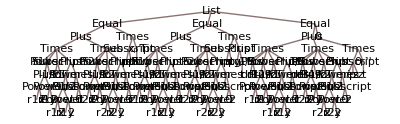

```mathematica
(*simpStep1//TreeForm*)
```

```mathematica
(simpStep2=(simpStep1//.terms3)//Simplify)//MatrixForm(*//TraditionalForm*)
```

((r1x k_1 (a-L0_1))/(√(a^2))+(r2x k_2 (b-L0_2))/(√(b^2))==m_p x_p''[t]
(r1y k_1 (a-L0_1))/(√(a^2))+(r2y k_2 (b-L0_2))/(√(b^2))==m_p (g+y_p''[t])
(c1 k_1 (a-L0_1))/(√(a^2))+(c2 k_2 (b-L0_2))/(√(b^2))+ⅈ_(p,zz) θ_p''[t]==0)

```mathematica
(simpStep3=Map[Map[Times[#,a b ]&,#]&,simpStep2]//Expand//Simplify)//MatrixForm
```

((√(a^2) b^2 r1x k_1 (a-L0_1)+a^2 √(b^2) r2x k_2 (b-L0_2))/(a b)==a b m_p x_p''[t]
(√(a^2) b^2 r1y k_1 (a-L0_1)+a^2 √(b^2) r2y k_2 (b-L0_2))/(a b)==a b m_p (g+y_p''[t])
(√(a^2) b^2 c1 k_1 (a-L0_1)+a^2 (√(b^2) c2 k_2 (b-L0_2)+b^2 ⅈ_(p,zz) θ_p''[t]))/(a b)==0)

```mathematica
simpStep3//.dispSimp//Expand//MatrixForm//TraditionalForm
```

(-(√(a^2) b k_1 L0_1 r1x)/a+√(a^2) b k_1 r1x-(a √(b^2) k_2 L0_2 r2x)/b+a √(b^2) k_2 r2x==a b m_p x_p''
-(√(a^2) b k_1 L0_1 r1y)/a+√(a^2) b k_1 r1y-(a √(b^2) k_2 L0_2 r2y)/b+a √(b^2) k_2 r2y==a b g m_p+a b m_p y_p''
-(√(a^2) b c1 k_1 L0_1)/a+√(a^2) b c1 k_1-(a √(b^2) c2 k_2 L0_2)/b+a √(b^2) c2 k_2+a b ⅈ_p θ_p''==0)

```mathematica
(simpStep4= Subscript[k, 1] b(a-Subscript[L0, 1])( {{r1x}, {r1y}, {c1}})+Subscript[k, 2] a(b-Subscript[L0, 1])( {{r2x}, {r2y}, {c2}})+({{0}, {-Subscript[m, p]g a b}, {0}})-a b ({{Subscript[m, p], 0, 0}, {0, Subscript[m, p], 0}, {0, 0, -Subscript[I, p]}}).({{Subscript[x, p]''[t]}, {Subscript[y, p]''[t]}, {Subscript[θ, p]''[t]}})-({{0}, {0}, {0}}))//MatrixForm
```

(b r1x k_1 (a-L0_1)+a r2x k_2 (b-L0_1)-a b m_p x_p''[t]
b r1y k_1 (a-L0_1)+a r2y k_2 (b-L0_1)-a b g m_p-a b m_p y_p''[t]
b c1 k_1 (a-L0_1)+a c2 k_2 (b-L0_1)+a b ⅈ_p θ_p''[t])

```mathematica
terms2//.dispSimp//MatrixForm//TraditionalForm
terms3//.dispSimp//MatrixForm//TraditionalForm
```

(l_p c(θ_p)+h_p s(θ_p)-2 x_p+2 x_1→2 r1x
-1/2 h_p c(θ_p)+1/2 l_p s(θ_p)-y_p+y_1→r1y
1/2 h_p c(θ_p)-1/2 l_p s(θ_p)+y_p-y_1→-r1y
-1/2 l_p c(θ_p)+1/2 h_p s(θ_p)-x_p+x_2→r2x
-1/2 h_p c(θ_p)-1/2 l_p s(θ_p)-y_p+y_2→r2y
h_p c(θ_p)+l_p s(θ_p)+2 y_p-2 y_2→-2 r2y
l_p ((y_1-y_p) c(θ_p)+x_1 (-s(θ_p))+x_p s(θ_p))→dr1
h_p (x_1 c(θ_p)-x_p c(θ_p)+(y_1-y_p) s(θ_p))→dr2
h_p (x_2 c(θ_p)-x_p c(θ_p)+(y_2-y_p) s(θ_p))→dr4
l_p ((y_p-y_2) c(θ_p)+x_2 s(θ_p)-x_p s(θ_p))→dr3)

(√(r1x^2+r1y^2)→a
√(r2x^2+r2y^2)→b
dr1+dr2→2 c1
dr3+dr4→2 c2
r1x^2+r1y^2→a^2
r2x^2+r2y^2→b^2
√(a^2)→a
√(b^2)→b)

```mathematica
Subscript[x, p],Subscript[y, p],Subscript[θ, p]=f(Subscript[x, 1],Subscript[y, 1],Subscript[x, 2],Subscript[y, 2],Subscript[k, 1],Subscript[k, 2],Subscript[l, p],Subscript[h, p])
```

```mathematica
non-conver forces:
aerodynamic =  f(OverDot[Subscript[x, p]],OverDot[Subscript[y, p]],Subscript[θ, p], Subscript[w, x],Subscript[w, y]) , w for wind components. = f(Subscript[relV, x],Subscript[relV, y]) , relV is relative to air 
dumping = f(OverDot[Subscript[l, i]])=f(OverDot[Subscript[x, i]],OverDot[Subscript[y, i]],OverDot[Subscript[x, p]],OverDot[Subscript[y, p]])
```

what needs to be done in order to keep horizontal payload? :

```mathematica
simpStep1/.Subscript[θ, p][t]->0/.dispSimp//MatrixForm//TraditionalForm
```

((k_1 (√dom11-L0_1) (l_p-2 x_p+2 x_1))/(2 √dom11)+(k_2 (√dom22-L0_2) (-l_p/2-x_p+x_2))/(√dom22)==m_p x_p''
(k_1 (√dom11-L0_1) (-h_p/2-y_p+y_1))/(√dom11)+(k_2 (√dom22-L0_2) (-h_p/2-y_p+y_2))/(√dom22)==m_p (g+y_p'')
(k_1 (√dom11-L0_1) (h_p (x_1-x_p)+l_p (y_1-y_p)))/(2 √dom11)+(k_2 (√dom22-L0_2) (h_p (x_2-x_p)+l_p (y_p-y_2)))/(2 √dom22)+ⅈ_p θ_p''==0)

```mathematica
non-dimensional settings
```

```mathematica
OverTilde[Subscript[y, p]][t]=Subscript[y, p][t] Subscript[L0, 1]  or any other of the lengths varialbes
t=τ/Subscript[ω, s]
Subscript[ω, s]^2=(Subscript[k, 1]/Subscript[m, p])[g/l=1/s^2]
```

```mathematica
(* planar mass with springs *)
```

```mathematica
(trimmedEq=quadEqNominal/.{Subscript[x, 1]'[t]->0,Subscript[x, 2]'[t]->0,Subscript[x, 1]''[t]->0,Subscript[x, 2]''[t]->0,Subscript[θ, 1]'[t]->0,Subscript[θ, 2]'[t]->0,Subscript[θ, 1]''[t]->0,Subscript[θ, 2]''[t]->0,Subscript[θ, 1][t]->0,Subscript[θ, 2][t]->0})//MatrixForm//TraditionalForm
```

((k_1 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t)) (√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2)-L0_1))/(2 √(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2))+(k_2 (1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t)) (√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2)-L0_2))/(√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2))==m_p x_p''(t)
(k_1 (-1/2 h_p cos(θ_p(t))+1/2 l_p sin(θ_p(t))-y_p(t)+y_1(t)) (√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2)-L0_1))/(√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2))+(k_2 (-1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))-y_p(t)+y_2(t)) (√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2)-L0_2))/(√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2))==m_p (g+y_p''(t))
ⅈ_(p,zz) θ_p''(t)+(k_1 (h_p (x_1(t) cos(θ_p(t))-x_p(t) cos(θ_p(t))+(y_1(t)-y_p(t)) sin(θ_p(t)))+l_p (x_1(t) (-sin(θ_p(t)))+x_p(t) sin(θ_p(t))+(y_1(t)-y_p(t)) cos(θ_p(t)))) (√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2)-L0_1))/(2 √(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2))+(k_2 (h_p (x_2(t) cos(θ_p(t))-x_p(t) cos(θ_p(t))+(y_2(t)-y_p(t)) sin(θ_p(t)))+l_p (x_2(t) sin(θ_p(t))-x_p(t) sin(θ_p(t))+(y_p(t)-y_2(t)) cos(θ_p(t)))) (√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2)-L0_2))/(2 √((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2))==0)

```mathematica
eq2D={trimmedEq[[1]]}/.Subscript[θ, p][t]->0/.Subscript[y, 1][t]->0/.Subscript[y, 2][t]->0/.Subscript[y, p][t]->0/.Subscript[l, p]->0/.Subscript[h, p]->0/.dispSimp//Expand//Simplify//TraditionalForm
```

{(k_1 ((x_1-x_p)^2-L0_1 √((x_1-x_p)^2)))/(x_1-x_p)+(k_2 ((x_2-x_p)^2-L0_2 √((x_2-x_p)^2)))/(x_2-x_p)==m_p x_p''}

case for elastic pendulum:

```mathematica
in 2D case the 2DOF are x,Subscript[y, p], looking at lumped mass payload.
Subscript[X, 1],Subscript[X, 2]->0,Subscript[k, 2]->0,l,Subscript[h, p]->0 as well
```

```mathematica
L2D=L/.{Subscript[x, 1][t]->0,Subscript[x, 1]'[t]->0,Subscript[x, 1]''[t]->0,Subscript[x, 2][t]->0,Subscript[x, 2]'[t]->0,Subscript[x, 2]''[t]->0,Subscript[θ, 1]'[t]->0,Subscript[θ, 1]''[t]->0,Subscript[θ, 2]'[t]->0,Subscript[θ, 2]''[t]->0,Subscript[θ, 1][t]->0,Subscript[θ, 2][t]->0}/.{Subscript[y, 1][t]->0,Subscript[y, 1]'[t]->0,Subscript[y, 1]''[t]->0,Subscript[y, 2][t]->0,Subscript[y, 2]'[t]->0,Subscript[y, 2]''[t]->0}/.Subscript[l, p]->0/.Subscript[h, p]->0/.Subscript[k, 2]->0(*/.Subscript[θ, p][t]->0*)
```

-g m_p y_p[t]-1/2 k_1 (-L0_1+√(x_p[t]^2+y_p[t]^2))^2+1/2 m_p (x_p'[t]^2+y_p'[t]^2)+1/2 ⅈ_(p,zz) θ_p'[t]^2

```mathematica
L2D=L/.{Subscript[x, 1][t]->0,Subscript[x, 1]'[t]->0,Subscript[x, 1]''[t]->0,Subscript[x, 2][t]->0,Subscript[x, 2]'[t]->0,Subscript[x, 2]''[t]->0,Subscript[θ, 1]'[t]->0,Subscript[θ, 1]''[t]->0,Subscript[θ, 2]'[t]->0,Subscript[θ, 2]''[t]->0,Subscript[θ, 1][t]->0,Subscript[θ, 2][t]->0}/.{Subscript[y, 1][t]->0,Subscript[y, 1]'[t]->0,Subscript[y, 1]''[t]->0,Subscript[y, 2][t]->0,Subscript[y, 2]'[t]->0,Subscript[y, 2]''[t]->0}/.Subscript[l, p]->0/.Subscript[h, p]->0/.Subscript[k, 2]->0(*/.Subscript[θ, p][t]->0*)
```

```mathematica
(quadEqNominal2D=EulerEquations[L2D,{Subscript[x, p][t],Subscript[y, p][t],Subscript[θ, p][t]},t](*[[All,1]]*)(*==Q*)//Expand//Simplify)/.dispSimp//MatrixForm//TraditionalForm
```

(k_1 x_p (L0_1/(√(x_p^2+y_p^2))-1)==m_p x_p''
k_1 y_p (L0_1/(√(x_p^2+y_p^2))-1)==m_p (g+y_p'')
ⅈ_p θ_p''==0)

```mathematica
quadEqNominal2DEquib=quadEqNominal2D/.{Subscript[x, p]''[t]->0,Subscript[y, p]''[t]->0}
```

{k_1 x_p[t] (-1+L0_1/(√(x_p[t]^2+y_p[t]^2)))==0,k_1 y_p[t] (-1+L0_1/(√(x_p[t]^2+y_p[t]^2)))==g m_p,ⅈ_(p,zz) θ_p''[t]==0}

```mathematica
Solve[quadEqNominal2DEquib,{Subscript[x, p][t],Subscript[y, p][t](*,Subscript[θ, p][t]*)}]
```

{{x_p[t]→0,y_p[t]→(-k_1 L0_1-g m_p)/k_1},{x_p[t]→0,y_p[t]→(k_1 L0_1-g m_p)/k_1}}

```mathematica
Subscript[y, p][t]->-Subscript[L0, 1]-g Subscript[m, p]/Subscript[k, 1]
OverTilde[Subscript[y, p]][t]->-1-g/Subscript[L0, 1] Subscript[m, p]/Subscript[k, 1]=-1-B
```

```mathematica
Solve[a x^2+b x+c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
s
```

```mathematica
equibState={Subscript[x, p][t]->0+epsX, Subscript[y, p][t]->-Subscript[L0, 1]-g Subscript[m, p]/Subscript[k, 1]+epsY}
quadEqNominal2D/.equibState
```

{x_p[t]→epsX,y_p[t]→epsY-L0_1-(g m_p)/k_1}

{epsX k_1 (-1+L0_1/(√(epsX^2+(epsY-L0_1-(g m_p)/k_1)^2)))==m_p x_p''[t],k_1 (epsY-L0_1-(g m_p)/k_1) (-1+L0_1/(√(epsX^2+(epsY-L0_1-(g m_p)/k_1)^2)))==m_p (g+y_p''[t]),ⅈ_(p,zz) θ_p''[t]==0}

```mathematica
Series[Sin[x+y], {x,0,3},{y,0,3}]
```

(y-y^3/6+O[y]^4)+(1-y^2/2+O[y]^4) x+(-y/2+y^3/12+O[y]^4) x^2+(-1/6+y^2/12+O[y]^4) x^3+O[x]^4

```mathematica
Series[f[y,x], {x,0,5},{y,0,5}]
```

(f[0,0]+f^(1,0)[0,0] y+1/2 f^(2,0)[0,0] y^2+1/6 f^(3,0)[0,0] y^3+1/24 f^(4,0)[0,0] y^4+1/120 f^(5,0)[0,0] y^5+O[y]^6)+(f^(0,1)[0,0]+f^(1,1)[0,0] y+1/2 f^(2,1)[0,0] y^2+1/6 f^(3,1)[0,0] y^3+1/24 f^(4,1)[0,0] y^4+1/120 f^(5,1)[0,0] y^5+O[y]^6) x+(1/2 f^(0,2)[0,0]+1/2 f^(1,2)[0,0] y+1/4 f^(2,2)[0,0] y^2+1/12 f^(3,2)[0,0] y^3+1/48 f^(4,2)[0,0] y^4+1/240 f^(5,2)[0,0] y^5+O[y]^6) x^2+(1/6 f^(0,3)[0,0]+1/6 f^(1,3)[0,0] y+1/12 f^(2,3)[0,0] y^2+1/36 f^(3,3)[0,0] y^3+1/144 f^(4,3)[0,0] y^4+1/720 f^(5,3)[0,0] y^5+O[y]^6) x^3+(1/24 f^(0,4)[0,0]+1/24 f^(1,4)[0,0] y+1/48 f^(2,4)[0,0] y^2+1/144 f^(3,4)[0,0] y^3+1/576 f^(4,4)[0,0] y^4+(f^(5,4)[0,0] y^5)/2880+O[y]^6) x^4+(1/120 f^(0,5)[0,0]+1/120 f^(1,5)[0,0] y+1/240 f^(2,5)[0,0] y^2+1/720 f^(3,5)[0,0] y^3+(f^(4,5)[0,0] y^4)/2880+(f^(5,5)[0,0] y^5)/14400+O[y]^6) x^5+O[x]^6

```mathematica
nn=1; Series[f[y,x], {x,0,nn},{y,0,nn}]
```

(f[0,0]+f^(1,0)[0,0] y+O[y]^2)+(f^(0,1)[0,0]+f^(1,1)[0,0] y+O[y]^2) x+O[x]^2

```mathematica
nn=1; Series[√f[y,x], {x,0,nn},{y,0,nn}]
```

(√f[0,0]+(f^(1,0)[0,0] y)/(2 √f[0,0])+O[y]^2)+((f^(0,1)[0,0])/(2 √f[0,0])+(-(f^(0,1)[0,0] f^(1,0)[0,0])/(4 f[0,0]^(3/2))+(f^(1,1)[0,0])/(2 √f[0,0])) y+O[y]^2) x+O[x]^2

```mathematica
√(Subscript[x, p]^2+Subscript[y, p]^2)=√(Subscript[x, p]^2+Subscript[y, p]^2)+(2 Subscript[x, p])/(2 √(Subscript[x, p]^2+Subscript[y, p]^2))y+(2 Subscript[y, p])/(2 √(Subscript[x, p]^2+Subscript[y, p]^2))x+O(ϵ)
```

```mathematica
Series[f[x], {x,0,5}]
```

f[0]+f'[0] x+1/2 f''[0] x^2+1/6 f^(3)[0] x^3+1/24 f^(4)[0] x^4+1/120 f^(5)[0] x^5+O[x]^6

```mathematica
Series[√f[x], {x,0,5}]
```

√f[0]+(f'[0] x)/(2 √f[0])+((-f'[0]^2+2 f[0] f''[0]) x^2)/(8 f[0]^(3/2))+((3 f'[0]^3-6 f[0] f'[0] f''[0]+4 f[0]^2 f^(3)[0]) x^3)/(48 f[0]^(5/2))+((-15 f'[0]^4+36 f[0] f'[0]^2 f''[0]-12 f[0]^2 f''[0]^2-16 f[0]^2 f'[0] f^(3)[0]+8 f[0]^3 f^(4)[0]) x^4)/(384 f[0]^(7/2))+((105 f'[0]^5-300 f[0] f'[0]^3 f''[0]+180 f[0]^2 f'[0] f''[0]^2+120 f[0]^2 f'[0]^2 f^(3)[0]-80 f[0]^3 f''[0] f^(3)[0]-40 f[0]^3 f'[0] f^(4)[0]+16 f[0]^4 f^(5)[0]) x^5)/(3840 f[0]^(9/2))+O[x]^6

```mathematica
Series[quadEqNominal2D[[1]], {Subscript[x, p][t],0,3},{Subscript[y, p][t],0,3}]//Simplify
```

((k_1 L0_1)/y_p[t]-k_1+O[y_p[t]]^4) x_p[t]+(-(k_1 L0_1)/(2 y_p[t]^3)+O[y_p[t]]^4) x_p[t]^3+O[x_p[t]]^4==m_p x_p''[t]

```mathematica
Series[quadEqNominal2D[[1]], {Subscript[y, p][t],0,3},{Subscript[x, p][t],0,3}]//Simplify
```

(k_1 L0_1-k_1 x_p[t]+O[x_p[t]]^4)+(-(k_1 L0_1)/(2 x_p[t]^2)+O[x_p[t]]^4) y_p[t]^2+O[y_p[t]]^4==m_p x_p''[t]

```mathematica
Series[Subscript[L0, 1]/(√((Subscript[x, p][t])^2+(Subscript[y, p][t])^2)),{Subscript[x, p][t],0,3},{Subscript[y, p][t],0,3}]//Expand//Simplify
```

(L0_1/y_p[t]+O[y_p[t]]^4)+(-L0_1/(2 y_p[t]^3)+O[y_p[t]]^4) x_p[t]^2+O[x_p[t]]^4

```mathematica
trials:
```

```mathematica
Series[f[x],{x,a,3}]
```

f[a]+f'[a] (x-a)+1/2 f''[a] (x-a)^2+1/6 f^(3)[a] (x-a)^3+O[x-a]^4

```mathematica
Subscript[Delta, Equilibrium]=(Subscript[m, p] g)/Subscript[k, i]
```

```mathematica
equalibriumTerms={
Subscript[x, 1]'[t]->0,Subscript[x, 1]''[t]->0,
Subscript[x, 2]'[t]->0,Subscript[x, 2]''[t]->0,
Subscript[θ, 1]'[t]->0,Subscript[θ, 1]''[t]->0,
Subscript[θ, 2]'[t]->0,Subscript[θ, 2]''[t]->0,
Subscript[y, 1]'[t]->0,Subscript[y, 1]''[t]->0,
Subscript[y, 2]'[t]->0,Subscript[y, 2]''[t]->0,
Subscript[x, p]'[t]->0,Subscript[x, p]''[t]->0,
Subscript[y, p]'[t]->0,Subscript[y, p]''[t]->0,
Subscript[θ, p]'[t]->0,Subscript[θ, p]''[t]->0
}
```

{x_1'[t]→0,x_1''[t]→0,x_2'[t]→0,x_2''[t]→0,θ_1'[t]→0,θ_1''[t]→0,θ_2'[t]→0,θ_2''[t]→0,y_1'[t]→0,y_1''[t]→0,y_2'[t]→0,y_2''[t]→0,x_p'[t]→0,x_p''[t]→0,y_p'[t]→0,y_p''[t]→0,θ_p'[t]→0,θ_p''[t]→0}

```mathematica
simpStep1/.equalibriumTerms//.dispSimp//MatrixForm//TraditionalForm
```

((k_1 r1x (√(r1x^2+r1y^2)-L0_1))/(√(r1x^2+r1y^2))+(k_2 r2x (√(r2x^2+r2y^2)-L0_2))/(√(r2x^2+r2y^2))==0
(k_1 r1y (√(r1x^2+r1y^2)-L0_1))/(√(r1x^2+r1y^2))+(k_2 r2y (√(r2x^2+r2y^2)-L0_2))/(√(r2x^2+r2y^2))==g m_p
(k_1 (dr1+dr2) (√(r1x^2+r1y^2)-L0_1))/(2 √(r1x^2+r1y^2))+(k_2 (dr3+dr4) (√(r2x^2+r2y^2)-L0_2))/(2 √(r2x^2+r2y^2))==0)

```mathematica
Subscript[k, i]->Infinity
```

k_i→∞

```mathematica
? cable is a rod
```

```mathematica
X^(..)=f(X)
```